```mathematica
target[x_]:=f[x]
range2={-10, 10, 0.1};
```

```mathematica
xVals=Range@@range2;
funcFromVals[vals_][x_]:=Quiet[Interpolation[Transpose[{xVals, vals}],InterpolationOrder->1][x], {InterpolatingFunction::dmval, InterpolatingFunction::dprec}]
```

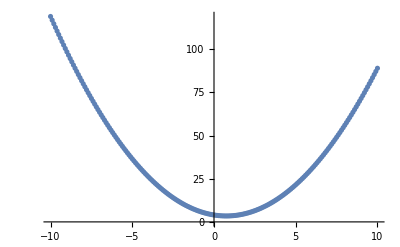

InterpolatingFunction::dmval: Input value {5.02611×10^18} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {5.02611×10^18} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {4.81995×10^18} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dprec: The precision of input value {4.81995×10^18} and/or the interpolation grid is insufficient to compute the value.

InterpolatingFunction::dmval: Input value {4.61625×10^18} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {4.61625×10^18} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

-Graphics-

```mathematica
funcVals=target/@xVals;
approxVals=approxFunc[approxFunc[#]]&/@xVals;
plots={};

pRange=AbsoluteOptions[Plot[target[x], {x, range2[[1]], range2[[2]]}, ImageSize->Medium],PlotRange][[1,2]];

PlotVals[vals_]:=Show[{ListPlot[Transpose[{xVals, vals}], PlotRange->pRange], Plot[funcFromVals[vals][x], {x, range2[[1]], range2[[2]]}, PlotRange->pRange]}]
PlotVals[funcVals]
PlotVals[approxVals]
```

```mathematica
imax=5;jmax=2; (* j is how many steps to run in between plots, i is how many plots to generate *)

progress=PrintTemporary["0% Complete"];
Table[Table[
approxFunc=funcFromVals[approxVals];
nestedApproxVals=approxFunc[approxFunc[#]]&/@xVals;
deltaVals=funcVals-nestedApproxVals;
newApproxVals=approxVals+0.1*deltaVals;
approxVals=newApproxVals;
NotebookDelete[progress];
progress=PrintTemporary[ToString[Floor[100*(i*jmax+j)/((imax+1)*(jmax))]]<>"% Complete"];,{j, jmax}];
plots=AppendTo[plots,Plot[approxFunc[approxFunc[x]], {x, range2[[1]], range2[[2]]}, ImageSize->Small, PlotRange->pRange]];
, {i,imax}];
```

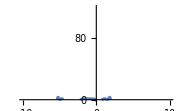
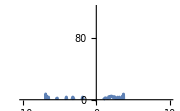
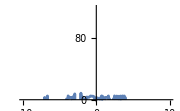
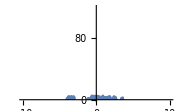
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots
```

-Graphics-approx

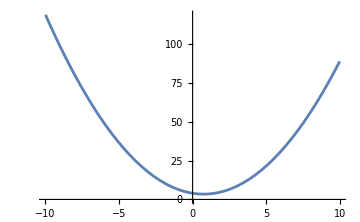
-Graphics-approx nested-Graphics-target

```mathematica
pSize=Medium;

pTarget=Plot[target[x], {x, range2[[1]], range2[[2]]}, ImageSize->pSize];
pApprox=Plot[approxFunc[x], {x, range2[[1]], range2[[2]]}, ImageSize->pSize];
pApproxNested=Plot[approxFunc[approxFunc[x]], {x, range2[[1]], range2[[2]]}, ImageSize->pSize, PlotRange->pRange];

Labeled[pApprox, "approx"]
Row[{Labeled[pApproxNested, "approx nested"], Labeled[pTarget, "target"]}]
```